```mathematica
nBandits=10;
steps=1000;
runs=2000;
```

```mathematica
ensembleAverageReward=ConstantArray[0,steps];
ensembleOptimal=ConstantArray[0,steps];
Monitor[Do[banditMeans=RandomVariate[NormalDistribution[0,1],nBandits];
bandits=NormalDistribution[#,1]&/@banditMeans;
means=ConstantArray[0,nBandits];
rewards=ConstantArray[0,nBandits];
actions=ConstantArray[0,nBandits];
optimalBandit=FirstPosition[banditMeans,Max[banditMeans]][[1]];
{averageReward,optimal}=Reap[Do[greedyChoice=FirstPosition[means,Max[means]][[1]];
actions[[greedyChoice]]+=1;
reward=RandomVariate[bandits[[greedyChoice]]];
rewards[[greedyChoice]]+=reward;
means[[greedyChoice]]=rewards[[greedyChoice]]/actions[[greedyChoice]];
Sow[Total[rewards]/t,"average"];
Sow[actions[[optimalBandit]]/t,"optimal"],{t,steps}],{"average","optimal"}][[2,All,1]];
ensembleAverageReward+=averageReward;
ensembleOptimal+=optimal,{r,runs}],{r,t}]
ensembleAverageReward/=runs;
ensembleOptimal/=runs;
```

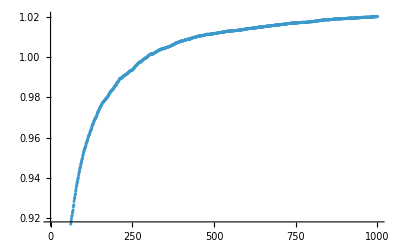

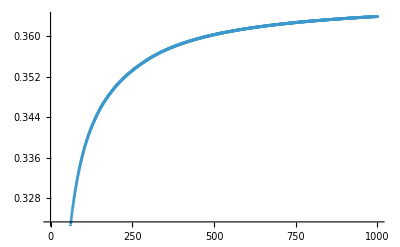

```mathematica
ListPlot[Table[{t,ensembleAverageReward[[t]]},{t,steps}]]
ListPlot[Table[{t,ensembleOptimal[[t]]},{t,steps}]]
```